# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\All models comparison

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Quantum channels

## Channel XXZ

```mathematica
?ClosedXXZHamiltonian
```

```mathematica
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
```

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψT={haar[L-1],Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],RandomChainProductState[L-1]};

tf=10.;
styles={Style["Haar, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["New random state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"StyleBox[\"t\",FontSlant->\"Italic\"] = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];
AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];
,{i,3}];
```

```mathematica
(*Test time*)
t=tf-0.1;
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],Show[purities[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testframe_closedXXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>".png",testimage];
```

```mathematica
grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],Show[purities[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
```

```mathematica
Table[Export["XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_frame_"<>ToString[i]<>".png",grids[[i]]],{i,Length[grids]}]
```

$Aborted

## Channel XXZ without Bloch sphere

-Graphics-

```mathematica
?ClosedXXZHamiltonian
```

```mathematica
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
```

```mathematica
L=6;
Δ=0.01;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=100;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ψT={haar[L-1],Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],RandomChainProductState[L-1]};
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,ψT[[1]]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,ψT[[2]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,ψT[[3]]]],{i,caometer}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

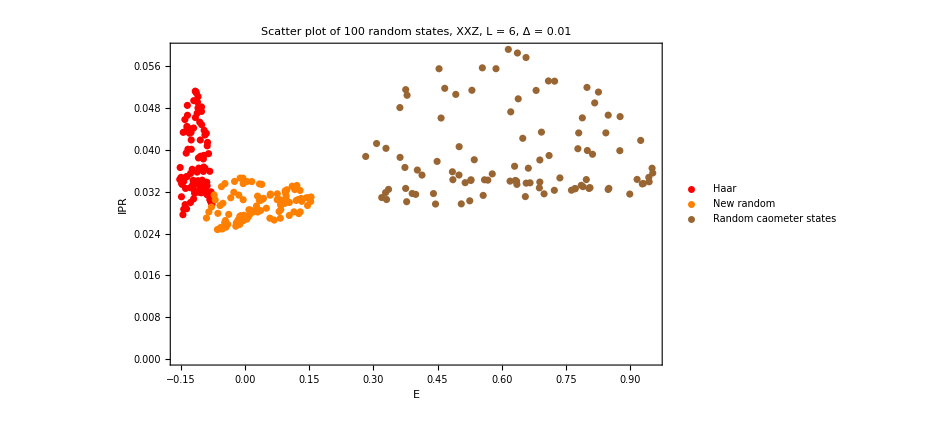

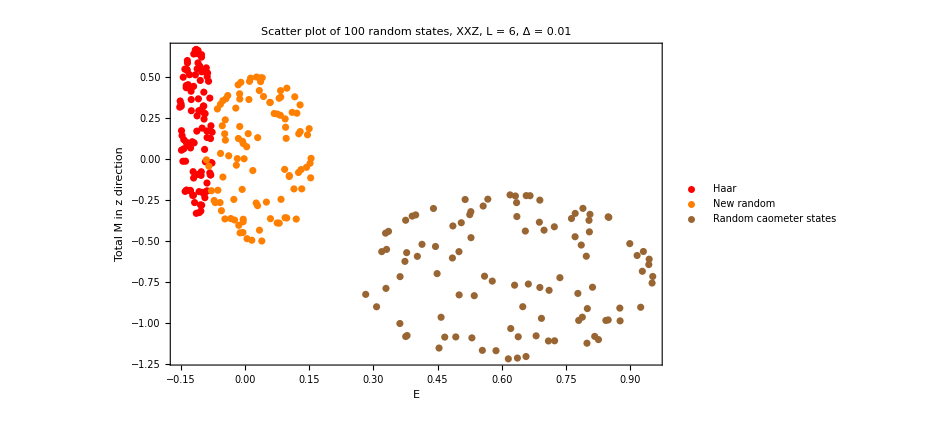

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
tf=50.;
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
```

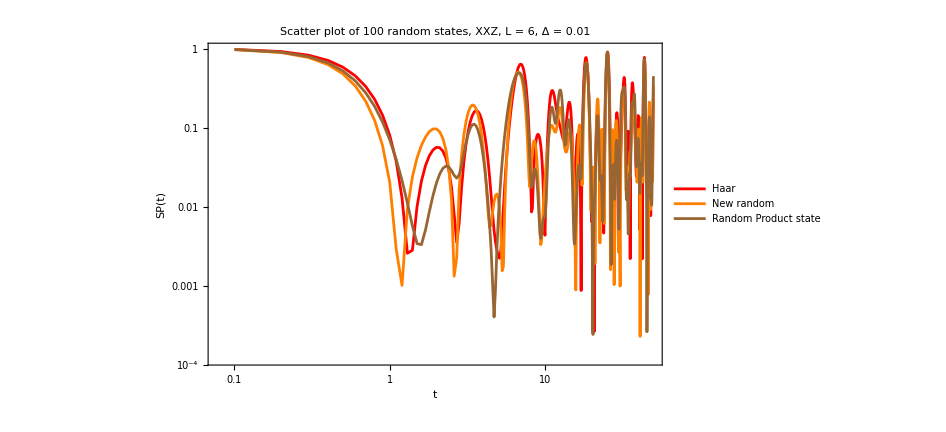

```mathematica
ListLogLogPlot[{Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}]}],Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}]}],Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

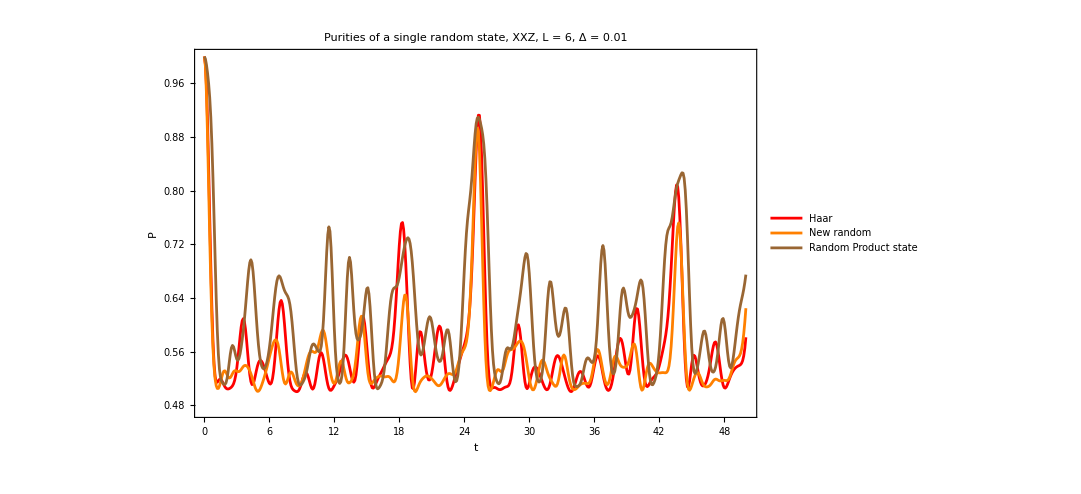

```mathematica
tlist=Range[0,tf,0.1];
purityplot=ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->800]
Export["purity_closedXXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>".png",purityplot];
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

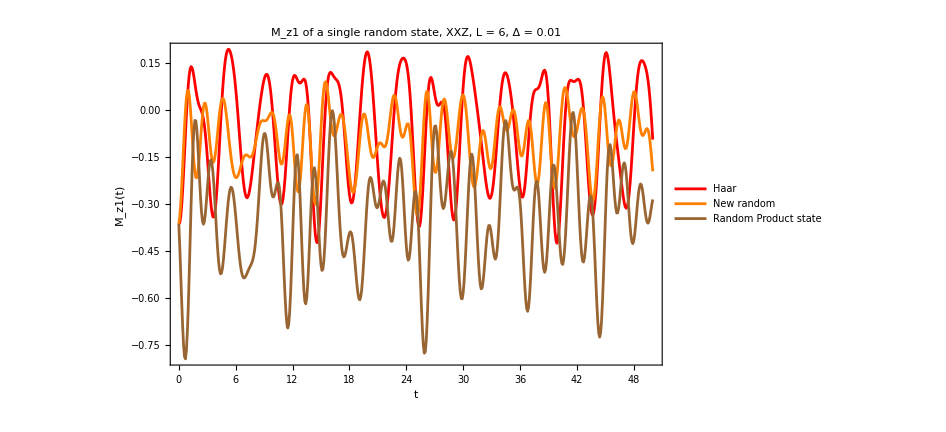

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

```mathematica
styles={Style["Haar, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["New random state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigenval,eigenvec,L];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];

AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];
,{i,3}];
```

```mathematica
reducedmags={ListPlot[Transpose[{tlist,reducedmaga}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagb}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Orange},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["New random",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]};
```

```mathematica
(*Test*)
testimage=Grid[Table[{listplots[[i]],purities[[i]],reducedmags[[i]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testframe_closedXXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>".png",testimage];
```

## Wisniacki without Bloch sphere

```mathematica
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
```

```mathematica
L=3;
hx=J=1.;
hz=4;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=500;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ψT={haar[L-1],Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],RandomChainProductState[L-1]};
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,ψT[[1]]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,ψT[[2]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,ψT[[3]]]],{i,caometer}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
ope2=KroneckerProduct[sz,IdentityMatrix[2^(L-1)]];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
singlemaga=Table[Chop[Conjugate[i].ope2.i],{i,ψa}];
singlemagb=Table[Chop[Conjugate[i].ope2.i],{i,ψb}];
singlemagc=Table[Chop[Conjugate[i].ope2.i],{i,ψc}];
```

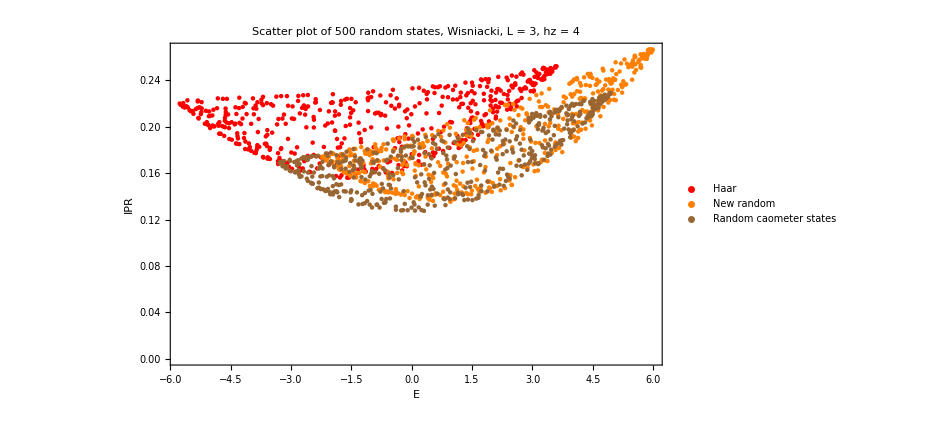

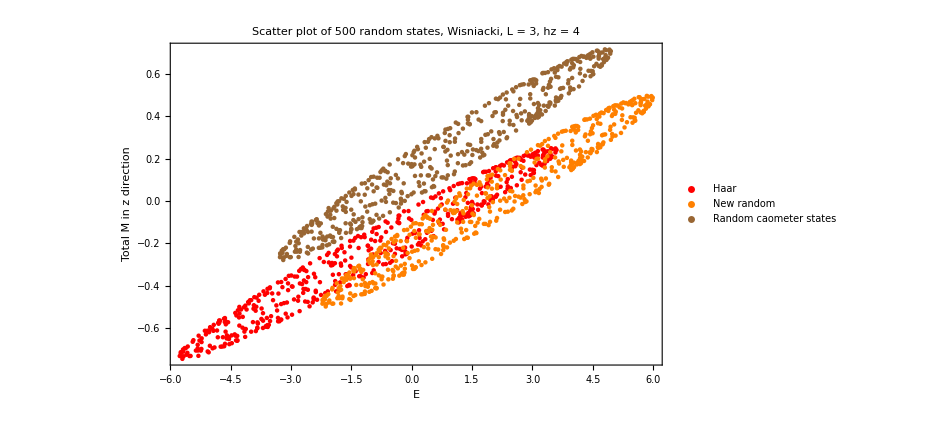

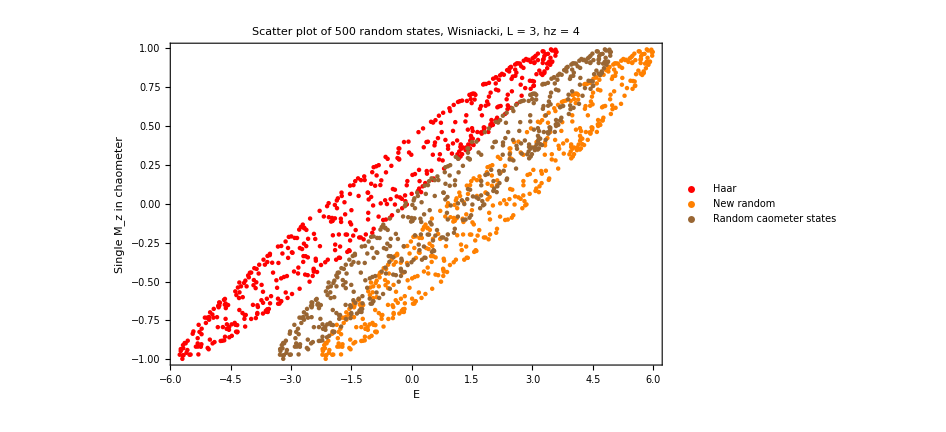

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,singlemaga}],Transpose[{energiesb,singlemagb}],Transpose[{energiesc,singlemagc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Single M_z in chaometer"]}]
```

```mathematica
tf=50.;
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
```

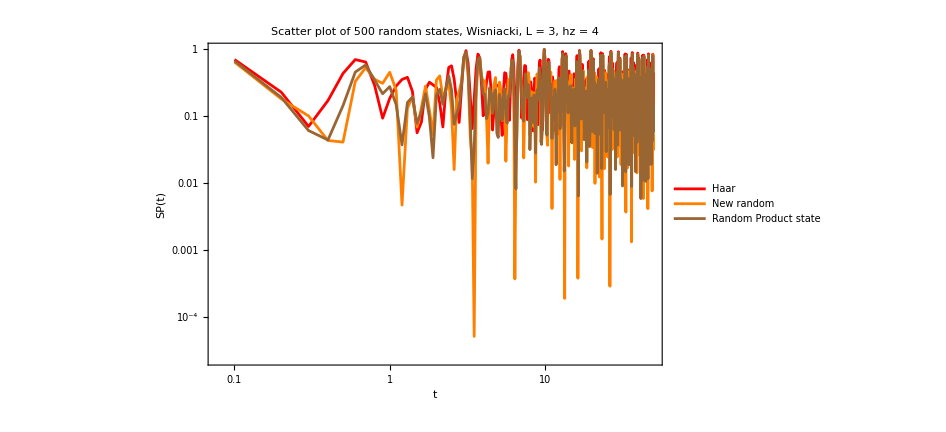

```mathematica
ListLogLogPlot[{Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}]}],Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}]}],Transpose[{Range[0,tf,0.1],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

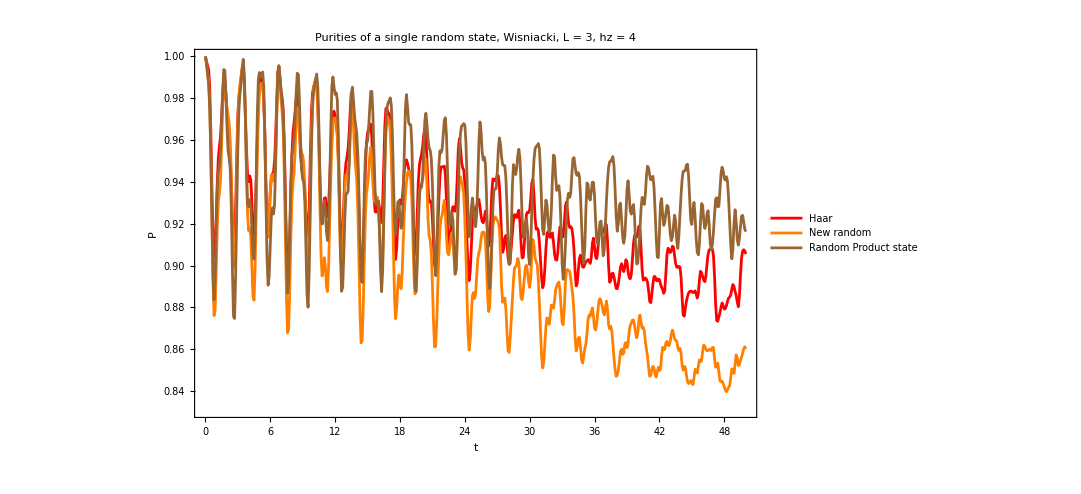

```mathematica
tlist=Range[0,tf,0.1];
purityplot=ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->800]
Export["purity_Wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",purityplot];
```

```mathematica
varza=Table[Chop[Tr[sz.i]]^2,{i,reduceda}];
varzb=Table[Chop[Tr[sz.i]]^2,{i,reducedb}];
varzc=Table[Chop[Tr[sz.i]]^2,{i,reducedc}];
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

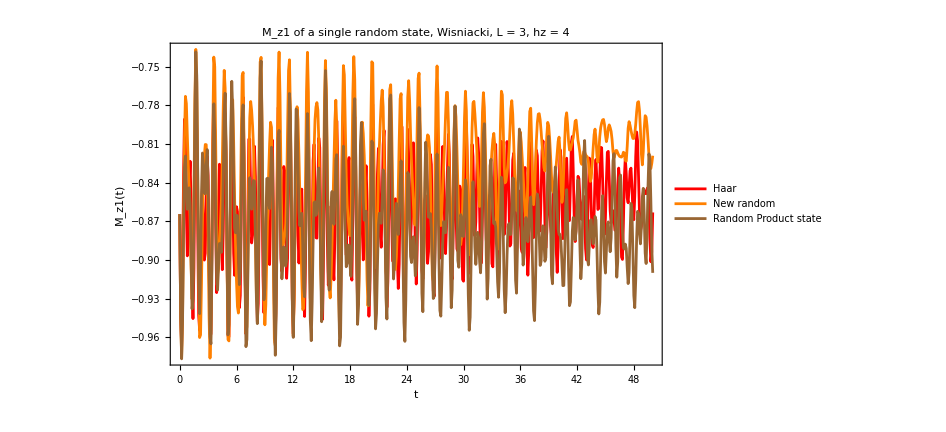

```mathematica
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

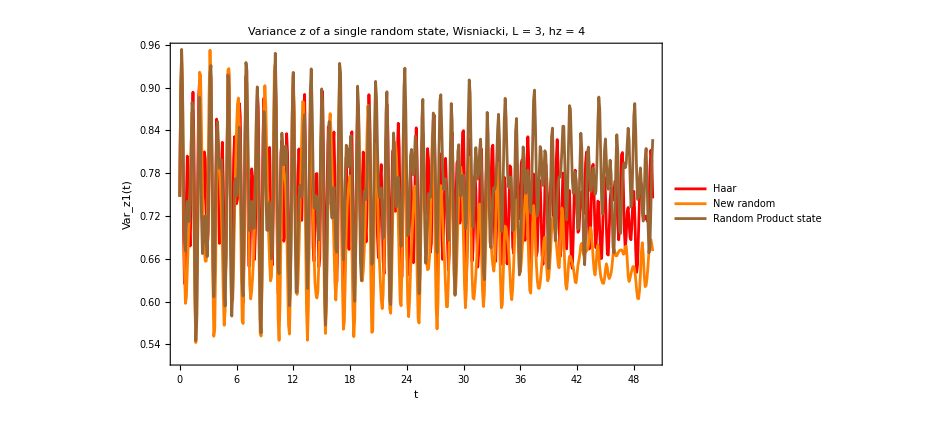

```mathematica
varianceplot=ListPlot[{Transpose[{tlist,varza}],Transpose[{tlist,varzb}],Transpose[{tlist,varzc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Variance z of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Var_z1(t)"]}]
Export["variancez_Wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",varianceplot];
```

```mathematica
styles={Style["Haar, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["New random state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black],Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
Do[
superOp=Superoperator[t,ψT[[i]],eigenval,eigenvec,L];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

,{t,0,tf,.1}];

AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];
,{i,3}];
```

```mathematica
reducedmags={ListPlot[Transpose[{tlist,reducedmaga}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagb}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Orange},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["New random",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]};
```

```mathematica
(*Test*)
testimage=Grid[Table[{listplots[[i]],purities[[i]],reducedmags[[i]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testframe_Wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage];
```